```mathematica
SetDirectory[NotebookDirectory[]];
```

```mathematica
Get["../lib/lib2.m"];
Get["../lib/util.m"];
```

$N::shdw: Symbol $N appears in multiple contexts {BFSS2`,Global`}; definitions in context BFSS2` may shadow or be shadowed by other definitions.

$K::shdw: Symbol $K appears in multiple contexts {BFSS2`,Global`}; definitions in context BFSS2` may shadow or be shadowed by other definitions.

```mathematica
plotsDir= "../../plots/plots-107";
If[!DirectoryQ[plotsDir], CreateDirectory[plotsDir]];
```

```mathematica
data = Import["../../runs/Trials/N5K9/24788149.dat"];
```

```mathematica
changeNK[5, 9];
```

```mathematica
$basisSU = $basisSU//Normal;
```

```mathematica
matdata = Monitor[Table[cMatOne[data[[ll]]], {ll, 1, Length[data]}], ProgressIndicator[(ll-1)/(Length[data]-1)]];
```

```mathematica
eig = Flatten@(Eigenvalues/@matdata[[All, 2]]);
```

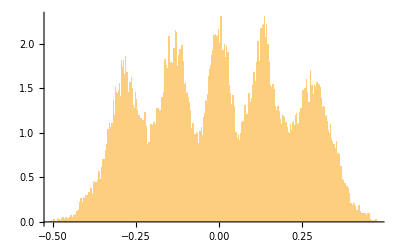

```mathematica
Histogram[eig, 300, PDF]
```

```mathematica
unitMats = (#-1/($N)Tr[#]IdentityMatrix[$N])&/@RandomVariate[GaussianUnitaryMatrixDistribution[1, $N], Length[data]];
```

```mathematica
unitEigs = Flatten[Eigenvalues/@unitMats];
```

```mathematica
(*unitMatsTrLess = (#-1/($N)Tr[#]IdentityMatrix[$N])&/@RandomVariate[GaussianUnitaryMatrixDistribution[1, $N], 100000];*)
```

```mathematica
(*unitEigsTrLess = Flatten[Eigenvalues/@unitMatsTrLess];*)
```

```mathematica
plt2 = Histogram[{eig,Standardize[unitEigs]}, 300, PDF,
ChartLegends->{"Simulation", "Traceless GUE"},
AxesLabel->{"eigenvalue", "PDF"},
PlotLabel->"Distribution of Eigenvalues of X1 across time",
ImageSize->600
];
```

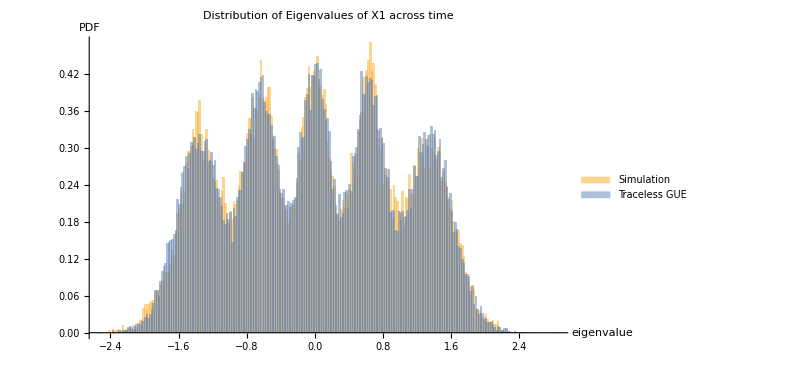

```mathematica
plt2
```

```mathematica
Export[plotsDir<>"/eigDist-TracelessGUE.pdf", Rasterize[plt2, ImageResolution->300, ImageSize->500]]
```

../../plots/plots-105/eigDist-TracelessGUE.pdf

```mathematica
plts=Table[Module[{},(
Print["Generating data n = "<>ToString@n];
obsSim[n]=Tr[MatrixPower[#,n]]&/@matdata[[All,2]]//Chop//Re;
obsUnitary[n]=Tr[MatrixPower[#,n]]&/@unitMatsTrLess//Chop//Re;
Print["Generating plot n = "<>ToString@n];
Histogram[{Standardize[obsSim[n]],Standardize[obsUnitary[n]]},3000,PDF,ImageSize->500,PlotLabel->"Tr[\!\(\*SuperscriptBox[\(X\),n]\)]; n = "<>ToString[n],ChartLegends->Placed[{"Simulation","Traceless GUE"},Bottom]]
)],{n,2,12}];

Print["Generating the full plot"];
plt=Framed[Column[{Style["Comparing with Traceless Gaussian Unitary Matrix Distribution",Darker@Blue,Bold,16],GraphicsGrid[ArrayReshape[plts,{4,3}],Frame->All,ImageSize->2000]},Alignment->Center],FrameMargins->10];

Print["Exporting"];
Export[plotsDir<>"/trXn-dist-tracelessGUE.pdf",Rasterize[plt,ImageResolution->300,ImageSize->500]];

Print["Done"];
```

Generating data n = 2

Generating plot n = 2

Generating data n = 3

Generating plot n = 3

Generating data n = 4

Generating plot n = 4

Generating data n = 5

Generating plot n = 5

Generating data n = 6

Generating plot n = 6

Generating data n = 7

Generating plot n = 7

Generating data n = 8

Generating plot n = 8

Generating data n = 9

Generating plot n = 9

Generating data n = 10

Generating plot n = 10

Generating data n = 11

Generating plot n = 11

Generating data n = 12

Generating plot n = 12

Generating the full plot

Exporting

Done